```mathematica
f[x_]:=-(0.4893-0.000753x)+√((0.4893-0.000753x)^2+0.00147x)
```

```mathematica
g[x_]:=√((f[x]^2+1.954f[x]+0.00151f[x]+0.9546+0.00147+1.954)^2-4(2f[x]^3+5.862f[x]^2+5.728f[x]+0.00294f[x]+1.865+0.00287))
```

```mathematica
g[x]
```

√((2.91007+1.95551 (-0.4893+√((0.4893-0.000753 x)^2+0.00147 x)+0.000753 x)+(-0.4893+√((0.4893-0.000753 x)^2+0.00147 x)+0.000753 x)^2)^2-4 (1.86787+5.73094 (-0.4893+√((0.4893-0.000753 x)^2+0.00147 x)+0.000753 x)+5.862 (-0.4893+√((0.4893-0.000753 x)^2+0.00147 x)+0.000753 x)^2+2 (-0.4893+√((0.4893-0.000753 x)^2+0.00147 x)+0.000753 x)^3))

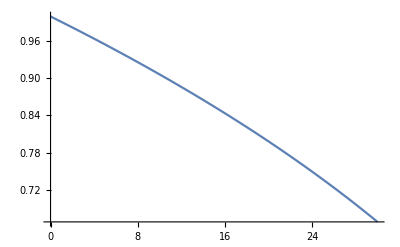

```mathematica
Plot[g[x],{x,0,30}]
```

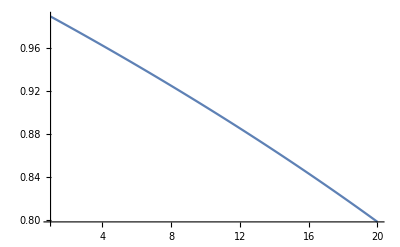

```mathematica
Plot[g[x],{x,1,20}]
```

```mathematica
Solve[((2.91007+1.9555099999999999 (-0.4893+√((0.4893-0.000753 x)^2+0.00147 x)+0.000753 x)+(-0.4893+√((0.4893-0.000753 x)^2+0.00147 x)+0.000753 x)^2)^2-4 (1.86787+5.7309399999999995 (-0.4893+√((0.4893-0.000753 x)^2+0.00147 x)+0.000753 x)+5.862 (-0.4893+√((0.4893-0.000753 x)^2+0.00147 x)+0.000753 x)^2+2 (-0.4893+√((0.4893-0.000753 x)^2+0.00147 x)+0.000753 x)^3))==0,x]
```

{{x→52.439},{x→4309.14}}

```mathematica
g[4.5]
```

0.958317